```mathematica
Quit
```

## Triángulos Numéricos

### Carga de Soluciones

```mathematica
(*Kottler*)
fKot[x_]:=1-1/x-x^2Λb/3/.Λb->1.5*10^(-32)
fUKot[u_]:=(fKot[1/u]);(*Cambio de x->1/u*)
(*Schwarzschild*)
fSch[x_]:=1-1/x
fUSch[u_]:=fSch[1/u]
(*Solucion Asimptotica*)
fAsimp[x_,λ_]:=1-(x^2 Λ)/3+(36531648 λ^2 Λ)/(x^9 (3+16 λ Λ^2)^5)+(2916 λ)/(x^6 (3+16 λ Λ^2)^3)-(1512 λ Λ)/(x^4 (3+16 λ Λ^2)^3)-3/(x (3+16 λ Λ^2))+(1536 (-(1863 λ)/(128 (3+16 λ Λ^2)^3)-(17037 λ^2 Λ^2)/(4 (3+16 λ Λ^2)^3)))/(x^7 (3+16 λ Λ^2)^2)/.Λ->1.5*10^(-32)
```

```mathematica
Rute="C:\\Users\\flavi\\OneDrive\\Escritorio\\Research\\CubicGravity\\Triangulos\\Data\\Datos_SgrA";(*Ruta para obtener Datos*)
Files=FileNames["*.dat",Rute]; (*Nombre*)
ImportedData=Table[Import[Files[[i]]],{i,1,Length[Files]}]; (*Importar datos*)
(*Valores de Lambda que estamos usando*)
λvals=Import["C:\\Users\\flavi\\OneDrive\\Escritorio\\Research\\CubicGravity\\Triangulos\\Data\\lambda_Vals.dat"]//Flatten;
```

```mathematica
(*Interpolacion de Funciones y unión de la fAsimp*)
FunSgrA[x_]:=Table[Interpolation[ImportedData[[i]]][x],{i,1,Length[λvals]}]
fUECG[u_]:=FunSgrA[1/u]
```

```mathematica
ListPlot[ImportedData]
```

-Graphics-

### Creación de Triángulos

```mathematica
Θ=0.3; (*Angle Shift*) (*Para el Sol Θ=0.3, b=RSun/rsSuun, δ=1.27,ϕmin=Θ, b1=2 b*)
b=4;(*Parámetro de Impacto*) 
ϵ=1/b; (*El inverso del parámetro de Impacto*)
(*δ=1.27;(*Desplazamiento angular para los lados adyacentes*) (*Para grafico es con 1.22, para triangulos es 1.27*)*)
ϕmin=Θ; (*π/2-δ*)(*ángulo inicial para lado izquierdo*)
ϕmax=π-ϕmin;(*ángulo inicial para lado derecho*)
b1= 1.5 b ;(*Para tablas es de 1.5*)
ϵ1= 1/b1;(*parámetro de impacto de los lados adyacentes*)
δval=10^-7;
n=7;(*Precision para la condición inicial. A mayor precisión solo se obtiene un número*)
```

#### Kottler Triangle

0.298484

{{u→InterpolatingFunction[…]}}

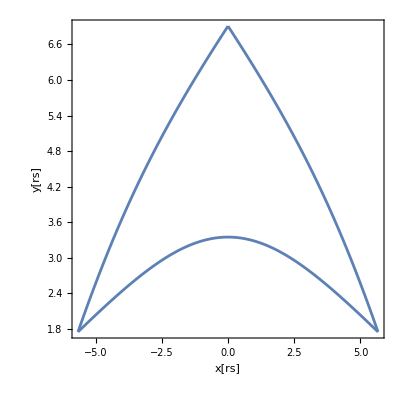

```mathematica
u0=Floor[(FindRoot[ϵ^2-fUKot[u]*u^2==0,{u,ϵ}][[1,2]] )*10^n]/10^n//N(*Condición donde u'[π/2]==0*)
(*Geodesica Pricipal (Base de Triángulo)*)
C1PhiMinKot=NDSolve[{(u'[ϕ])^2-ϵ^2+fUKot[u[ϕ]]*u[ϕ]^2==0,u[π/2+δval]==u0},u,{ϕ,π/2+δval,Θ},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->45]
C1PhiMaxKot = NDSolve[{(u'[ϕ])^2-ϵ^2+fUKot[u[ϕ]]*u[ϕ]^2==0,u[π/2-δval]==u0},u,{ϕ,π/2-δval,π-Θ},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->45];
(*Lados Adyacentes de triángulos*)
C2Kot=NDSolve[{(u'[ϕ])^2==ϵ1^2-fUKot[u[ϕ]]*u[ϕ]^2,u[ϕmin]==(u[ϕ]/.C1PhiMinKot/.ϕ->ϕmin)[[1]]},u,{ϕ,ϕmin,π/2},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->45];
C3Kot = NDSolve[{(u'[ϕ])^2==ϵ1^2-fUKot[u[ϕ]]*u[ϕ]^2,u[ϕmax]==(u[ϕ]/.C1PhiMaxKot/.ϕ->ϕmax)[[1]]},u,{ϕ,π/2,ϕmax},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->45];
(*Ploting*)
PltC1Kot=Show[ParametricPlot[{1/u[ϕ] Cos[ϕ],1/u[ϕ] Sin[ϕ]}/.C1PhiMaxKot,{ϕ,π/2,π-Θ}],ParametricPlot[{1/u[ϕ] Cos[ϕ],1/u[ϕ] Sin[ϕ]}/.C1PhiMinKot,{ϕ,π/2,Θ}],PlotRange->All,AspectRatio->1,Frame->True,FrameLabel->{"x[rs]","y[rs]"}];
PltC2Kot=ParametricPlot[{1/u[ϕ] Cos[ϕ],1/u[ϕ] Sin[ϕ]}/.C2Kot,{ϕ,ϕmin,π/2}];
PltC3Kot = ParametricPlot[{1/u[ϕ] Cos[ϕ],1/u[ϕ] Sin[ϕ]}/.C3Kot,{ϕ,π/2,ϕmax}];
YLim =(( 1/u[ϕ]Sin[ϕ])*(1.001)/.C2Kot/.ϕ->π/2)[[1]]; YLimInf = (1/u[ϕ]Sin[ϕ]*(0.999)/.C1PhiMinKot/.ϕ->π/2)[[1]];
XLimL = ((1/u[ϕ] Cos[ϕ])*(1.001)/.C3Kot/.ϕ->ϕmax)[[1]]; XLimR=((1/u[ϕ] Cos[ϕ])*(1.001)/.C2Kot/.ϕ->ϕmin)[[1]];
(*Plot final del triángulo*)
KotTri=Show[PltC1Kot,PltC2Kot, PltC3Kot,AspectRatio->1,(*PlotRange->{{XLimL,XLimR},{Automatic}}{YLimInf,YLim}},*)Frame->True,FrameLabel->{"x[rs]","y[rs]"}]
```

#### Schwarzschild Triangulo

```mathematica
s0=FindRoot[ϵ^2-fUSch[u]*u^2==0,{u,ϵ}][[1,2]] ;(*Condición donde u'[π/2]==0*)
s1=Floor[s0*10^n]/10^n//N;
(*Geodesica Pricipal (Base de Triángulo)*)
(*Hay que poner manualmente el valor de u0 en la condición inicial*)
C1PhiMinSch=NDSolve[{(u'[ϕ])^2-ϵ^2+fUSch[u[ϕ]]*u[ϕ]^2==0,u[π/2+δval]==s1},u,{ϕ,π/2+δval,Θ},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->45];
C1PhiMaxSch = NDSolve[{(u'[ϕ])^2-ϵ^2+fUSch[u[ϕ]]*u[ϕ]^2==0,u[π/2-δval]==s1},u,{ϕ,π/2-δval,π-Θ},Method->{"EquationSimplification"->"Residual"}];
(*Lados Adyacentes de triángulos*)
C2Sch=NDSolve[{(u'[ϕ])^2==ϵ1^2-fUSch[u[ϕ]]*u[ϕ]^2,u[ϕmin]==(u[ϕ]/.C1PhiMinSch/.ϕ->ϕmin)[[1]]},u,{ϕ,ϕmin,π/2},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->45];
C3Sch = NDSolve[{(u'[ϕ])^2==ϵ1^2-fUSch[u[ϕ]]*u[ϕ]^2,u[ϕmax]==(u[ϕ]/.C1PhiMaxSch/.ϕ->ϕmax)[[1]]},u,{ϕ,π/2,ϕmax},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->45];
```

#### Einstein Cubic Gravity Triangle

```mathematica
(*Triángulo Einstein Cubic Gravity, λ=0.05*)
u0ECG=Table[FindRoot[ϵ^2-fUECG[u][[i]]*u^2==0,{u,ϵ}][[1,2]],{i,1,Length[fUECG[x]]}];
u0ECGLessPrecision=Floor[u0ECG*10^n]/10^n//N;
(*Bases del triángulo*)
C1PhiMinECG=Table[NDSolve[{(u'[ϕ])^2-ϵ^2+(fUECG[u[ϕ]])[[i]]*u[ϕ]^2==0,u[π/2+δval]==u0ECGLessPrecision[[i]]},u,{ϕ,π/2+δval,Θ},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->45],{i,1,Length[fUECG[x]]}]

C1PhiMaxECG = Table[NDSolve[{u'[ϕ]^2-ϵ^2+(fUECG[u[ϕ]][[i]])*u[ϕ]^2==0,u[π/2-δval]==u0ECGLessPrecision[[i]]},u,{ϕ,π/2-δval,π-Θ},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->45],{i,1,Length[fUECG[x]]}];

(*Lados Adyacentes*)
C3ECG=Table[NDSolve[{(u'[ϕ])^2==ϵ1^2-(fUECG[u[ϕ]][[i]])*u[ϕ]^2,u[ϕmax]==((u[ϕ]/.C1PhiMaxECG[[i]]/.ϕ->ϕmax))[[1]]},u,{ϕ,ϕmax,π/2},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->45],{i,1,Length[fUECG[x]]}];C2ECG=Table[NDSolve[{(u'[ϕ])^2==ϵ1^2-(fUECG[u[ϕ]][[i]])*u[ϕ]^2,u[ϕmin]==(u[ϕ]/.C1PhiMinECG[[i]]/.ϕ->ϕmin)[[1]]},u,{ϕ,ϕmin,π/2},Method->{"EquationSimplification"->"Residual"},PrecisionGoal->45],{i,1,Length[fUECG[x]]}];
```

{{{u→InterpolatingFunction[…]}},{{u→InterpolatingFunction[…]}},{{u→InterpolatingFunction[…]}},{{u→InterpolatingFunction[…]}},{{u→InterpolatingFunction[…]}},{{u→InterpolatingFunction[…]}},{{u→InterpolatingFunction[…]}},{{u→InterpolatingFunction[…]}},{{u→InterpolatingFunction[…]}},{{u→InterpolatingFunction[…]}},{{u→InterpolatingFunction[…]}}}

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

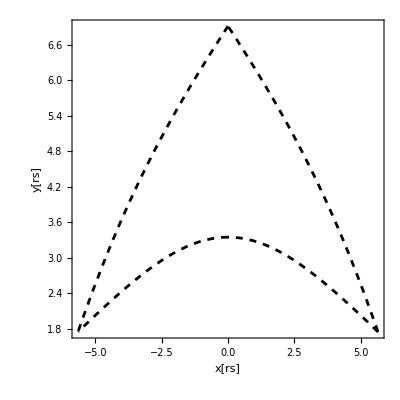
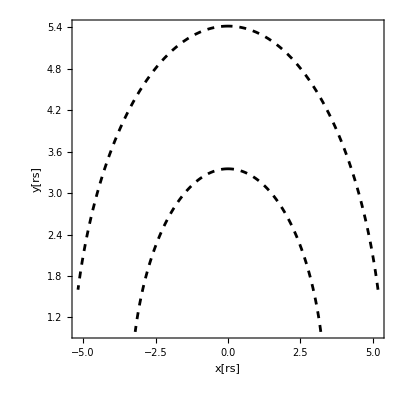
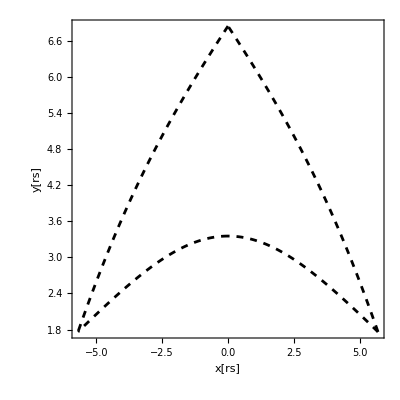
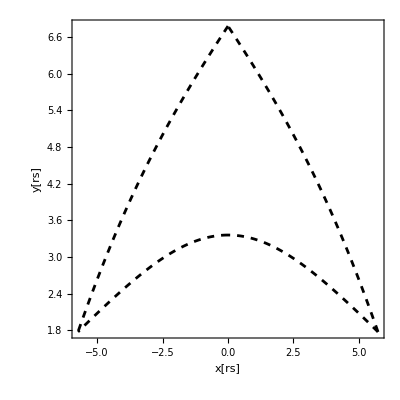
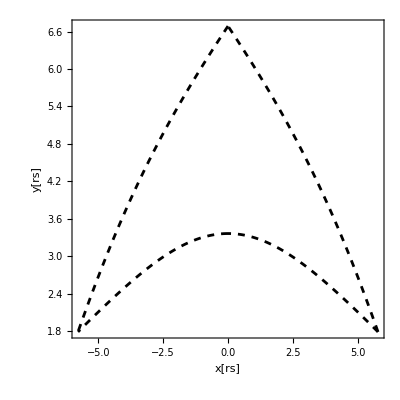
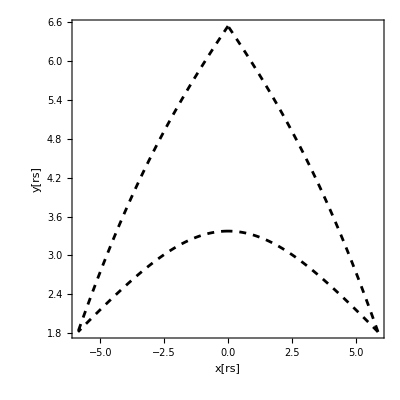
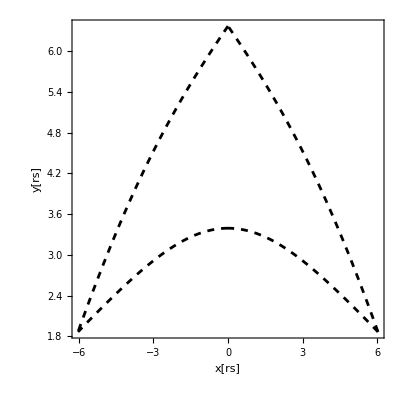
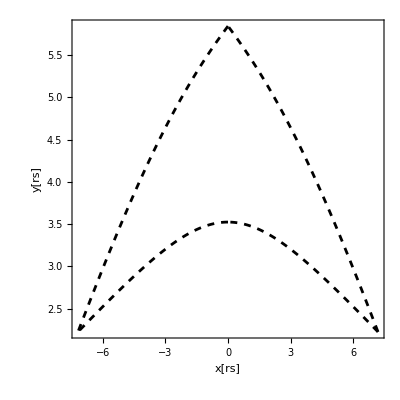

```mathematica
(*Ploting*)
PltC1ECG=Table[Show[ParametricPlot[{1/u[ϕ] Cos[ϕ],1/u[ϕ] Sin[ϕ]}/.C1PhiMinECG[[i]],{ϕ,π/2,Θ},PlotStyle->{Black,Dashed}],ParametricPlot[{1/u[ϕ] Cos[ϕ],1/u[ϕ] Sin[ϕ]}/.C1PhiMaxECG[[i]],{ϕ,π/2,π-Θ},PlotStyle->{Black,Dashed}],AspectRatio->1,PlotRange->All,Frame->True,FrameLabel->{"x[rs]","y[rs]"}],{i,1,Length[fUECG[x]]}];
PltC3ECG=Table[ParametricPlot[{1/u[ϕ] Cos[ϕ],1/u[ϕ] Sin[ϕ]}/.C3ECG[[i]],{ϕ,π/2,ϕmax},AspectRatio->1,PlotStyle->{Black,Dashed}],{i,1,Length[fUECG[x]]}];
PltC2ECG =Table[ParametricPlot[{1/u[ϕ] Cos[ϕ],1/u[ϕ] Sin[ϕ]}/.C2ECG[[i]],{ϕ,π/2,ϕmin},AspectRatio->1,PlotStyle->{Black,Dashed}],{i,1,Length[fUECG[x]]}];
xmin=Table[(1/u[ϕ] Cos[ϕ] 1.001/.C3ECG[[i]]/.ϕ->ϕmax)[[1]],{i,1,Length[fUECG[x]]}]; xmax=Table[(1/u[ϕ] Cos[ϕ] 1.001/.C2ECG[[i]]/.ϕ->ϕmin)[[1]],{i,1,Length[fUECG[x]]}];
ymin = Table[(1/u[ϕ] Sin[ϕ] 0.999 /.C1PhiMinECG/.ϕ->π/2)[[1]],{i,1,Length[fUECG[x]]}];ymax = Table[(1/u[ϕ] Sin[ϕ] 1.001 /.C2ECG/.ϕ->π/2)[[1]],{i,1,Length[fUECG[x]]}];
ECGTrian=Table[Show[PltC1ECG[[i]],PltC3ECG[[i]],PltC2ECG[[i]],AspectRatio->1(*,PlotRange->{{xmin,xmax},{ymin,ymax}}*)],{i,1,Length[fUECG[x]]}] (*Plot Final del Triángulo*)
(*ECGFunctions = {C1PhiMinECG,C1PhiMaxECG,C3ECG,C2ECG};*)
```

### Diferencia Angular

```mathematica
(*β1=C3-C1|ϕmax  β2=C1-C2|ϕmin  β3=C2-C3|π/2*)
```

Power::infy: Infinite expression 1/0. encountered.

{{0.00001,163.596},{0.0215444,1640.42},{0.0464159,3365.05},{0.1,5851.28},{0.215443,10294.},{0.464159,16041.},{1.,40959.1},{2.15443,22849.1},{4.64159,29692.8},{10.,35979.7}}

C:\Users\flavi\OneDrive\Escritorio\Research\CubicGravity\Triangulos\Data\alfa_Kot.txt

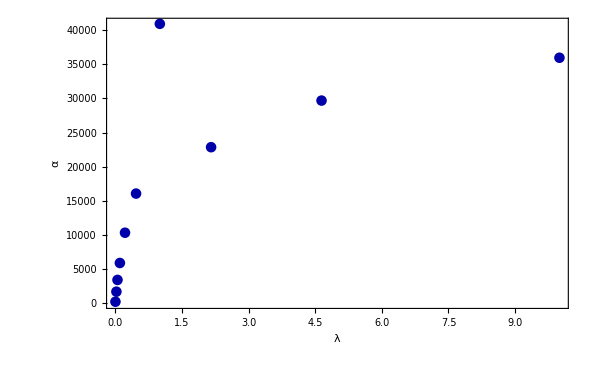

```mathematica
(*Suma Interna de Angulos Kottler*)
AngleKot[Sol_,ϕv_]:=3600*180/π (ArcTan[-u[ϕ] Sqrt[fUKot[u[ϕ]]]D[u[ϕ],ϕ]^(-1) ])/.Sol/.ϕ->ϕv;
β1Kot = (AngleKot[C3Kot,ϕmax]-AngleKot[C1PhiMaxKot,ϕmax]); 
β2Kot=(AngleKot[C1PhiMinKot,ϕmin]-AngleKot[C2Kot,ϕmin]); 
β3Kot = (AngleKot[C2Kot,π/2]-AngleKot[C3Kot,π/2]); 
βsKot=β1Kot+β2Kot+β3Kot;
(*Suma interna de Angulos Schwarzschild*)
AngleSch[Sol_,ϕv_]:=3600*180/π ArcTan[-u[ϕ] Sqrt[fUSch[u[ϕ]]]D[u[ϕ],ϕ]^(-1)]/.Sol/.ϕ->ϕv;
β1Sch=AngleSch[C3Sch,ϕmax]-AngleSch[C1PhiMaxSch,ϕmax];
β2Sch=AngleSch[C1PhiMinSch,ϕmin]-AngleSch[C2Sch,ϕmin];
β3Sch=AngleSch[C2Sch,π/2]-AngleSch[C3Sch,π/2];
βsSch=β1Sch+β2Sch+β3Sch;
(*Suma Interna de Angulos ECG*)
AngleECG[Sol_,ϕv_,i_]:=3600*180/π (ArcTan[-u[ϕ] Sqrt[fUECG[u[ϕ]][[i]]]D[u[ϕ],ϕ]^(-1) ])/.Sol/.ϕ->ϕv;
β1ECG=Table[AngleECG[C3ECG[[i]],ϕmax,i]-AngleECG[C1PhiMaxECG[[i]],ϕmax,i],{i,1,Length[fUECG[x]]}]//Flatten;
β2ECG=Table[AngleECG[C1PhiMinECG[[i]],ϕmin,i]-AngleECG[C2ECG[[i]],ϕmin,i],{i,1,Length[fUECG[x]]}]//Flatten;
β3ECG=Table[AngleECG[C2ECG[[i]],π/2,i]-AngleECG[C3ECG[[i]],π/2,i],{i,1,Length[fUECG[x]]}]//Flatten;
βsECG= β1ECG+β2ECG+β3ECG;
(*Angular Diference*)
αKot=Abs[βsKot[[1]]-βsECG];
αSch=Abs[βsSch[[1]]-βsECG];
αKot-αSch;
datosFiltrados=DeleteCases[Table[{λvals[[i]],αKot[[i]]},{i,1,Length[αKot]}],{_,Indeterminate}|{Indeterminate,_}]
Export["C:\\Users\\flavi\\OneDrive\\Escritorio\\Research\\CubicGravity\\Triangulos\\Data\\alfa_Kot.txt",datosFiltrados,"Table"]
ListPlot[Table[{λvals[[i]],αKot[[i]]},{i,1,Length[λvals]}],BaseStyle->14,Frame->True,FrameLabel->{"λ","α"},PlotStyle->Darker[Blue]]
```